```mathematica
To understand the surface level description of the different boxes, user is advised to refer to  "README_lock_opening.txt".
```

```mathematica
This file predicts the reversible reaction rates for the lock opening reaction BL+T <-> BT + L
```

Raw experimental data:

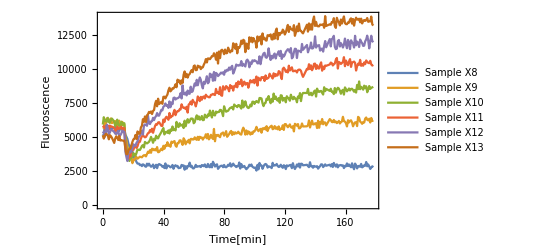

The [BL]o array will be:{9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398,9.64398}

Plot the converted data

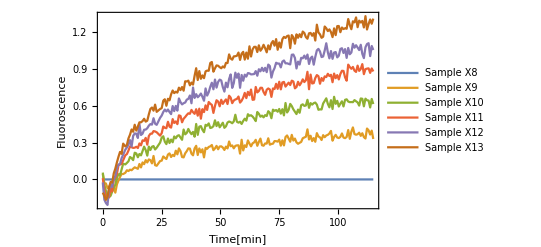

```mathematica
type=1;(*0 for M1/B1, 1 for M2/B1a M2, 2 for M3/B1b. Change this variable for B1, B1a, B1b*)
(*A single excel sheets contains lock opening experiemntal data fro B1, B1a and B1b*)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["1. Lock opening and binding"];

file="20220714 Lock opening B1 B1a B1b.xlsx";(*Name of the file that stores data for fluorescence vs time*)

data=Import[file,{"Sheets","Table All Cycles"}];

If[type==0,samp=Table[i,{i,1,6}],If[type==1,samp=Table[i,{i,8,13}],samp=Table[i,{i,15,20}]]];
(*sample of interest. {i,1,7} for B1; {i,8,14} for B1a; {i,15,21} for B1b*)
injinfo=0;(*If injinfo =0, use conc before injection and time as avg of before and after, else use conc after injection and time as after injection for 0*)
forward=1;(*1 if reaction forward going BL+T->BT+L, 0 otherwise*)

If[type==0,skip=0,If[type==1,skip=0,skip=0]];(*Data processing to remove erraneous datapoints*)
If[type==0,tend=500,If[type==1,tend=115,tend=115]];(*skip timesteps after injection or not*)
X1corr=0(*If 1, subtract sample X1 readings, else not*);

FBL=715.93;(*Fl density of BL/M1L/M1aL/M1bL*)
FBT=8075.9;(*Fl density of BT/M1T/M1sT/M1bT*)

(*Extract relevant data*)
For[i=1,i<=Length[data],i++,
If[data[[i]][[1]]=="Content",Break[]]]
data=data[[i;;,2;;]];
(* 
data has the following format: ;
For B1/M1: ;
Sample X1: 0nM T, X2: 2nM T, X3: 4nM T, X4: 6nM T, X5: 8nM T, X6: 10nM T, X7: pre-annealed BT complexes.;

For B1a/M1a-> Sample X8: 0nM T, X9: 2nM T, X10: 4nM T, X11: 6nM T, X12: 8nM T, X13: 10nM T, X14: pre-annealed BT complexes;

For B1b/M1b-> Sample X15: 0nM T, X16: 2nM T, X17: 4nM T, X18: 6nM T, X19: 8nM T, X20: 10nM T, X21: pre-annealed BT complexes;

Time[min] Sample X1 Sample X2 Sample X3 Sample X4 Sample X5 Sample X6...;
0 8983 9948 9248 9686 9373 9062...;
0.53 8696 9316 10039 9228 9138 9028...;
0.92 8647 9180 9539 9510 9125 9608...;
1.3 8820 9767 9968 9609 9353 9411...;s
*)
ff[x_]:=0;
(*Stores the legends in this variable*)
samplename=data[[1]][[2;;]];
legend={};(*will remove samples of insignificance from samplename array and be used as the legend list*)
For[i=1,i<=Length[samplename],i++,
If[samplename[[i]]=="Control C1"||samplename[[i]]=="Control C2"||samplename[[i]]=="Positive control P"||samplename[[i]]=="Negative control N",,
AppendTo[legend,samplename[[i]]];
]]

(*Extract column number of Control C2/Negative Control, Control C1/Positive Control, and row number of when Injection happened*)
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Control C2"||data[[1]][[i]]=="Negative control N",Break[]]]
iC2=i;
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Control C1"||data[[1]][[i]]=="Positive control P",Break[]]]
iC1=i;

(*Extract column number with 0nM injection*)
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Sample X1"&&type==0,Break[]];
If[data[[1]][[i]]=="Sample X8"&&type==1,Break[]];
If[data[[1]][[i]]=="Sample X15"&&type==2,Break[]];
]
iS0=i;

(*Also extract the column number with pre-annealed BT complexes (what does it mean)? for B1, B1a and B1b*)
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Sample X7",Break[]]];isat0=i;
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Sample X14",Break[]]];isat1=i;
For[i=1,i<=Length[data[[1]]],i++,
If[data[[1]][[i]]=="Sample X21",Break[]]];isat2=i;
(*Extract row number where injection happens*)
For[i=1,i<=Length[data],i++,
If[data[[i]][[2]]=="Inj.",Break[]]];
inj=i;(*injection row number*)
(***************************************************************************************)
(*Functions defined for further data processing*)
(*The "cut" function only takes data upto a certain time point and removes the rest*)
f[x_]:=0;
cut[x_,t_]:=(
For[i=1,i<=Length[x[[1]]],i++,
If[x[[1]][[i]][[1]]>t,Break[]];];
ret={};
For[j=1,j<=Length[x],j++,
AppendTo[ret,x[[j]][[1;;Min[i,Length[x[[j]]]]]]]];
Return[ret];
)
dnew=Array[f,Length[data[[1]]]-1];(*Stores all sample info*)
dnewfl=Array[f,Length[data[[1]]]-3];(*Stores all sample info minus controls*)
(***************************************************************************************)
(*Create a concentration array where each element stores a table of {time,fluoroscence} after injection for the different samples including +ve and -ve controls*)
For[i=2,i<=Length[data[[1]]],i++,
dnew[[i-1]]=data[[2;;,{1,i}]];
If[dnew[[i-1]][[inj-1]][[2]]=="Inj.",
If[injinfo==0,
dnew[[i-1]][[inj-1]][[2]]=dnew[[i-1]][[inj-2]][[2]]],
dnew[[i-1]][[inj-1]][[2]]=dnew[[i-1]][[inj]][[2]]];;
If[dnew[[i-1]][[inj-1]][[1]]==0.,(*If injection time = 0, use average of time before and after*)
If[injinfo==0,
dnew[[i-1]][[inj-1]][[1]]=0.5*(dnew[[i-1]][[inj-2]][[1]]+dnew[[i-1]][[inj]][[1]]),
dnew[[i-1]][[inj-1]][[1]]=dnew[[i-1]][[inj]][[1]];
];]]
(***************************************************************************************)
Print["Raw experimental data:"]
ListPlot[If[type==0,dnew[[samp]],dnew[[samp+2]]],Joined->True,PlotLegends->legend[[samp]],BaseStyle->FontSize[8],PlotRange->All,Frame->True,FrameLabel->{"Time[min]","Fluoroscence"},FrameStyle->Thick]

If[type==0,Export["Data//B1lockopen_Raw.wl",dnew[[samp]]],If[type==1,Export["Data//B1alockopen_Raw.wl",dnew[[samp]]],
Export["Data//B1blockopen_Raw.wl",dnew[[samp]]];
]];



(*Calculate the [ML]o from positive (control-negative control)/FBT*)
i=iC1-1;
dnewP=Table[{dnew[[i]][[j]][[1]]-If[injinfo==0,dnew[[i]][[inj-1]][[1]],dnew[[i]][[inj]][[1]]],(dnew[[i]][[j]][[2]]-dnew[[iC2-1]][[j]][[2]])/FBT},{j,If[injinfo==0,inj-1,inj],Length[dnew[[i]]],1}];
cbl=Mean[dnewP[[1;;,2]]];




(*Update the conc array baccording to [F(t)-X(0nM)(t)]/[P(t)-X(0nM)(t)] and using normalized time. Note inj-1 is impt bec inj was calculated on whole data, then the first name row was removed and inj. line was removed too*)
c=1; 
For[i=1,i<=Length[dnew],i++,
If[i==iC2-1||i==iC1-1||i==isat0-1||i==isat1-1||i==isat2-1,,
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-If[injinfo==0,dnew[[i]][[inj-1]][[1]],dnew[[i]][[inj]][[1]]],cbl*(dnew[[i]][[j]][[2]]-dnew[[iS0-1]][[j]][[2]])/(dnew[[iC1-1]][[j]][[2]]-dnew[[iS0-1]][[j]][[2]])(*-dnew[[iS0-1]][[j]][[2]]*)},{j,If[injinfo==0,inj-1,inj],Length[dnew[[i]]],1}];];
If[i==isat0-1||i==isat1-1||i==isat2-1,
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-If[injinfo==0,dnew[[i]][[inj-1]][[1]],dnew[[i]][[inj]][[1]]],cbl*(dnew[[i]][[j]][[2]]-dnew[[iS0-1]][[j]][[2]])/(dnew[[iC1-1]][[j]][[2]]-dnew[[iS0-1]][[j]][[2]])},{j,If[injinfo==0,inj-1,inj],Length[dnew[[i]]],1}];]]





ff[x_]:=cbl;
concBL=Array[ff,Length[dnewfl]-1];
Print["The [BL]o array will be:", concBL]
(*Skip the concentrations by specific steps and renormalize*)
For[j=1,j<=Length[dnewfl],j++,
skip0=skip;
If[skip>0,
tsub=dnewfl[[j]][[skip+1]][[1]];
csub=dnewfl[[j]][[skip+1]][[2]],
tsub=0;csub=0;];
For[i=skip+1,i<=Length[dnewfl[[j]]],i++,
dnewfl[[j]][[i]][[1]]=dnewfl[[j]][[i]][[1]]-tsub;
dnewfl[[j]][[i]][[2]]=dnewfl[[j]][[i]][[2]]-csub];
For[i=1,i<=skip,i++,
dnewfl[[j]]=Delete[dnewfl[[j]],1];]
];
dnewfl=cut[dnewfl,tend];

(*Plot the raw experimental data minus the negative control*)
dnewfl=dnewfl[[samp]];
Print["Plot the converted data"]
ListPlot[dnewfl,Joined->True,PlotLegends->legend[[samp]],BaseStyle->FontSize[8],PlotRange->All,Frame->True,FrameLabel->{"Time[min]","Fluoroscence"},FrameStyle->Thick]

If[type==0,Export["Data//B1lockopen.wl",dnewfl[[2;;6]]];
Export["Conc//B1Linitial.wl",concBL],If[type==1,Export["Data//B1alockopen.wl",dnewfl[[2;;6]]];
Export["Conc//B1aLinitial.wl",concBL],Export["Data//B1blockopen.wl",dnewfl[[2;;6]]];
Export["Conc//B1bLinitial.wl",concBL]]];
```

```mathematica
Start kinetic modeling. To fit the lock opening reaction, I will use a 2 parameter model BL+T <-> BT+L with rates k1, k2.
```

```mathematica
(*Import the time vs concentration data for different sample for B1L/B1aL/B1bL;
concC is the concentration of [BL]/[Ml];
concV is the concentraiton of [T].
*)
If[type==0,concC=Import["Conc//B1Linitial.wl"],If[type==1,concC=Import["Conc//B1aLinitial.wl"],concC=Import["Conc//B1bLinitial.wl"]]];
concV={2,4,6,8,10};(*variable concentration of [T]*)
If[type==0,data=Import["Data//B1lockopen.wl"],If[type==1,data=Import["Data//B1alockopen.wl"],data=Import["Data//B1blockopen.wl"]]];
Clear[t,k1,k2];

(*Function tabdfiff returns the difference in concentration between experimental dataset and predicted dataset*)
tab[y_,t_,k1_,k2_]:=(
q=t[[1;;,1]];
tabo={};
tabo=Table[{q[[i]],y[k1,k2][q[[i]]]/.sol[[j]]},{i,1,Length[q],1}];
Return[tabo];)
tabdiff[y_,t_,k1_,k2_]:=(p=tab[y,t,k1,k2];
p1=Table[p[[i]][[2]]-t[[i]][[2]],{i,1,Length[q],1}];
Return[p1];
)
ff[x_]:=0;
(*sol variable stores the parametric solution of the different differential equations*)
sol=Array[ff,Length[data]];
For[j=1,j≤Length[data],j++,
q=data[[j]][[1;;,1]];
sol[[j]]=ParametricNDSolve[{y'[t]==k1*(concC[[j]]-y[t])*(concV[[j]]-y[t])-k2*y[t](0.2*concC[[j]]+y[t]),y[0]==0},y,{t,q[[1]],q[[Length[q]]]},{k1,k2}]
]
```

```mathematica
(*Parameter fit model that minimizes MSD between experimental dataset and predicted model dataet*)

aa=AbsoluteTime[];
(*The model will take k(forward) and k(backward) from a space of different reaction rates.*)
If[type==0,
Tinterest=10;(*Important variable, all timesteps below this time are given a higher weight in calculating total MSD between experiment and model fit.*)
kstart=0.001;(*starting k for forward reaction*)
kend=.1;(*ending k for forward reaction*)
kstart2=.001;(*starting k for backward reaction*)
kend2=.1;(*ending k for backward reaction*)
,
If[type==1,(*For each type of monomer, the state space of k is different*)
Tinterest=150;
kstart=10^-4;
kend=10^-3;
kstart2=.005;
kend2=0.05;
,
Tinterest=80;
kstart=5*10^-4;
kend=5*10^-3;
kstart2=.005;
kend2=0.05;]]



fact=1.05;(*How often to increase k(forward). Should be greter than 1. The smaller this value, the more point in the state space will be considered*)
fact2=1.05;(*How often to increase k(backward)*)
No=IntegerPart[Log[(kend/kstart)]/Log[fact]]+1;(*Total points in the forward reaction rate state space to be considered*)
No2=IntegerPart[Log[(kend2/kstart2)]/Log[fact2]]+1;(*Total points in the backward reaction rate state space to be considered*)
Print["Number of datapoints sampled will be:", No*No2]
f0[x_,y_]:=0;

error=Array[f0,{No,No2}];(*Error is an array that stores the MSD error between experiments and model for each parameter set picked*)
error2={};(*error2 will store the best reaction rate predicted*)
c1=1;
result=0;
result2={kstart,kstart2};

(*Start the parameter estimation*)
For[k10=kstart,k10≤kend,k10=k10*fact,
c10=1;
For[k20=kstart2,k20≤kend2,k20=k20*fact2,
temp0=0;
(*Calculate the MSD error for each parameter set*)
For[j=1,j≤Length[data],j++,
temparr=tabdiff[y,data[[j]],k10,k20];
temp0+=RootMeanSquare[temparr];
For[i=1,i<=Length[temparr],i++,
sump=0;
If[data[[1]][[i]][[1]]>Tinterest,
sump+=0.2(temparr[[i]]*temparr[[i]]),
sump+=(temparr[[i]]*temparr[[i]])
];

temp0+=sump;

]];

temp=temp0;
If[c1==1 &&c10==1, result=temp];
error[[c1]][[c10++]]=temp;
error2=AppendTo[error2,{Log[k10],Log[k20],temp}];
(*If new difference between lists is small, remember that parameter set*)
If[temp<result,result=temp;result2={k10,k20}];
]c1++;
]
N[result2]
bb=AbsoluteTime[];
Print["Time taken:", bb-aa, "(sec)"];

(*Exports the reaction rates derived in .wl files*)
If[type==0,Export["Rates//B1klock.wl",result2],If[type==1,Export["Rates//B1aklock.wl",result2],Export["Rates//B1bklock.wl",result2]]];
```

Number of datapoints sampled will be:2304

{0.00032251,0.0055125}

Time taken:37.1681696(sec)

1.3321

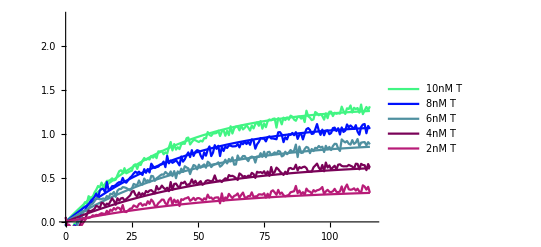

```mathematica
(*Shows the experimental data and best model fit*)
Cmax=Max[Flatten[data,1][[1;;,2]]]
tmax=Max[Flatten[data,1][[1;;,1]]];
reverse=1;
finplot[k_]:=(
SeedRandom[k+1];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[dnewfl],j++,
s1=ListPlot[data[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[If[reverse==1,y[result2[[1]],result2[[2]]][t]/.sol[[k]],y[result2[[1]]][t]/.sol[[k]]],{t,q[[1]],q[[Length[q]]]},PlotRange->{{0,tmax+1},{0,Cmax+1}},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[concV[[k]]]<>"nM T"}];
s2=Show[s2,s1];
Return[s2]])
Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]
```

```mathematica
Export the simulated and experimental data
```

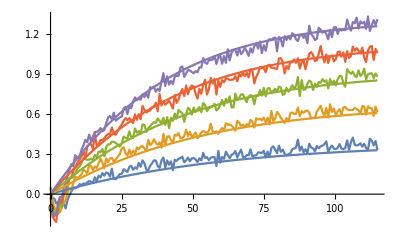

```mathematica
If[type==0,btype="B1"];
If[type==1,btype="B1a"];
If[type==2,btype="B1b"];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
lockexptdata=Import["1. Lock opening and binding\\Data\\"<>btype<>"lockopen.wl"];
concC=Import["1. Lock opening and binding\\Conc\\"<>btype<>"Linitial.wl"];
rates=Import["1. Lock opening and binding\\Rates\\"<>btype<>"klock.wl"];
concV={2,4,6,8,10};(*variable concentration*)
ff[x_]:=0;

(*stores the parametric solution of the different differential equations*)
sol=Array[ff,Length[lockexptdata]];
For[j=1,j≤Length[lockexptdata],j++,
q=lockexptdata[[j]][[1;;,1]];
sol[[j]]=ParametricNDSolve[{y'[t]==k1*(concC[[j]]-y[t])*(concV[[j]]-y[t])-k2*y[t](0.2*concC[[j]]+y[t]),y[0]==0},y,{t,q[[1]],q[[Length[q]]]},{k1,k2}]
]
data={};
For[i=1,i<=Length[lockexptdata],i++,
AppendTo[data,Table[{t,y[rates[[1]],rates[[2]]][t]/.sol[[i]]},{t,q[[1]],q[[Length[q]]]}]]]
s1=ListPlot[lockexptdata,Joined->True];
s2=ListPlot[data,Joined->True];
Show[s1,s2]
Export["1. Lock opening and binding\\Data\\Sim_"<>btype<>".wl",data];



SetDirectory[ParentDirectory[NotebookDirectory[]]];
lockexptdata=Import["1. Lock opening and binding\\Data\\"<>btype<>"lockopen_Raw.wl"];
ListPlot[lockexptdata,Joined->True]
qq={};
AppendTo[qq,lockexptdata[[1]][[1;;,1]]];
For[i=1,i<=Length[lockexptdata],i++,
AppendTo[qq,lockexptdata[[i]][[1;;,2]]]]
Export["Excel data\\Lock opening\\Cy3\\"<>btype<>"lockopen_Raw.xlsx",Transpose[qq]]
```